```mathematica
A=0.25;
b=0.2;
c=0.1;
d1=0.67;
d2=d1;
μ1=-0.043;
μ2=0;
μ3=μ2;
μ4=0.05;
μ5=μ4;

ϕ1[px_,py_,a_,l_]:=Exp[-ⅈ*l*(√3)/2 a(-px+√3 py)]
ϕ2[px_,py_,a_,l_]:=Exp[-ⅈ*l*(√3)/2 a(+px+√3 py)]
ϕ3[px_,py_,a_,l_]:=Exp[-ⅈ*l*3a*py]
W[l_]:=Exp[ⅈ*l*(2*π)/3]
P1A[px_,py_,a_]:={ⅈ*A*(ϕ3[px,py,a,1]-ϕ2[px,py,a,1]),b*ϕ3[px,py,a,1]+c*ϕ2[px,py,a,1],c*ϕ3[px,py,a,1]+b*ϕ2[px,py,a,1],d1*ϕ2[px,py,a,1],d2}
P2A[px_,py_,a_]:={ⅈ*A*(1-ϕ3[px,py,a,1]),W[1](b+c*ϕ3[px,py,a,1]),W[-1](c+b*ϕ3[px,py,a,1]),d1,d2}
P3A[px_,py_,a_]:={ⅈ*A*(ϕ2[px,py,a,1]-1),W[-1](c+b*ϕ2[px,py,a,1]),W[1](c*ϕ2[px,py,a,1]+b),d1*ϕ1[px,py,a,-1],d2}
P1B[px_,py_,a_]:={-ⅈ*A*(ϕ3[px,py,a,-1]-ϕ2[px,py,a,-1]),b*ϕ3[px,py,a,-1]+c*ϕ2[px,py,a,-1],c*ϕ3[px,py,a,-1]+b*ϕ2[px,py,a,-1],d2*ϕ2[px,py,a,-1],d1}
P2B[px_,py_,a_]:={-ⅈ*A*(1-ϕ3[px,py,a,-1]),W[-1](b+c*ϕ3[px,py,a,-1]),W[1](c+b*ϕ3[px,py,a,-1]),d2,d1}
P3B[px_,py_,a_]:={-ⅈ*A*(ϕ2[px,py,a,-1]-1),W[1](c+b*ϕ2[px,py,a,-1]),W[-1](c*ϕ2[px,py,a,-1]+b),d2*ϕ1[px,py,a,1],d1}
II={{μ1,0,0,0,0},{0,μ2,0,0,0},{0,0,μ3,0,0},{0,0,0,μ4,0},{0,0,0,0,μ5}};
H[px_,py_,a_]:=-(TensorProduct[P1A[px,py,a],P1B[px,py,a]]+TensorProduct[P2A[px,py,a],P2B[px,py,a]]+TensorProduct[P3A[px,py,a],P3B[px,py,a]])+II;
```

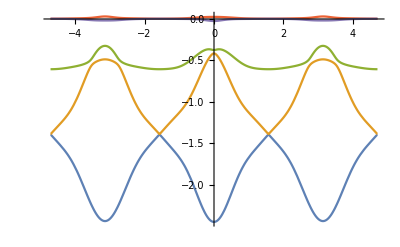

```mathematica
Plot[{Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[1]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[2]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[3]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[4]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[5]]},{θ,-1.5π,1.5π}]
```

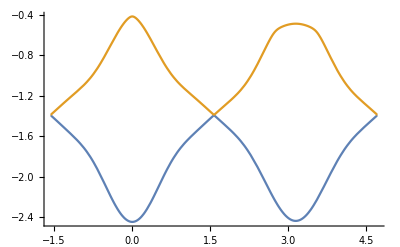

```mathematica
Plot[{Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[1]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[2]]},{θ,-0.5π,1.5π}]
```

```mathematica
Eigenvalues[H1[1,0,0]]
```

{0,0,0,0,2 (b^2+2 b c+c^2+d1 d2)}

```mathematica
TensorProduct[{1,0,1},{1,0,1}]
```

{{1,0,1},{0,0,0},{1,0,1}}